# Practical 7 :

## Solve the system of ordinary differential equations of the type dx/dt = ax + by, x(0) = x_0 dy/dt = ax + by, y(0) = y_0

```mathematica
sol = DSolve[{D[x[t],t]==a*x[t]+b*y[t],D[y[t],t]==a*x[t]+b*y[t], x[0]== p,y[0]== q},{x[t],y[t]},t]
```

{{x[t]→(b p+a ⅇ^((a+b) t) p-b q+b ⅇ^((a+b) t) q)/(a+b),y[t]→(-a p+a ⅇ^((a+b) t) p+a q+b ⅇ^((a+b) t) q)/(a+b)}}

```mathematica
x[t_] = x[t]/.sol /.{a->1,b->1,p->1,q->2}
```

{1/2 (-1+3 ⅇ^(2 t))}

```mathematica
y[t_] = y[t]/.sol /.{a->1,b->1,p->1,q->2}
```

{1/2 (1+3 ⅇ^(2 t))}

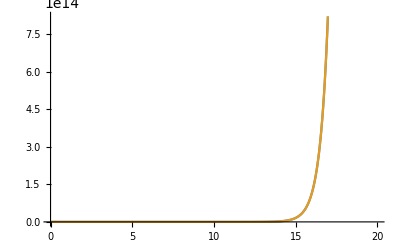

```mathematica
Plot[{x[t],y[t]},{t,0,20}]
```

```mathematica
x[t_] = x[t]/.sol /.{a->1,b->1,p->10,q->20}
y[t_] = y[t]/.sol /.{a->1,b->1,p->10,q->20}
```

{1/2 (-10+30 ⅇ^(2 t))}

{1/2 (10+30 ⅇ^(2 t))}

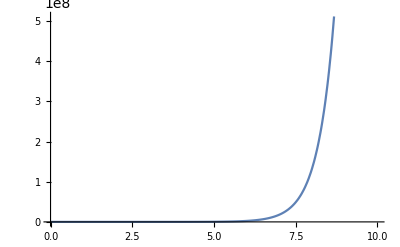

```mathematica
Plot[%,{t,0,10}]
```

```mathematica
(* For various values of constants we can find the solution of system of ODE given. *)
```